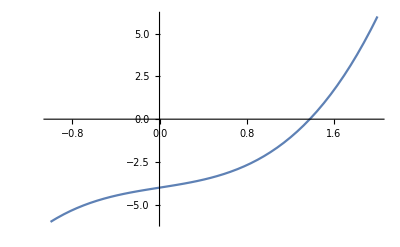

```mathematica
f[x_]:=x^3+x-4;
a=-1;b=2;
Plot[f[x],{x,a,b}]
```

```mathematica
(*So the function is continuous and differentiable in the interval*)
NSolve[f'[c]==(f[b]-f[a])/(b-a)&&c∈Interval[{a,b}],c]
```

{{c→{-1.}},{c→{1.}}}

```mathematica
Exit[]
```